```mathematica
localdir = "C:\\Users\\tramiada\\OneDrive\\Projects\\gen_spe\\Figure3\\";
```

## Figure 3

```mathematica
ps3  = {{Black,AbsoluteDashing[{15,5}],AbsoluteThickness[th]},{Gray,AbsoluteDashing[{15,5}],AbsoluteThickness[th]}};
```

### Figure 3a

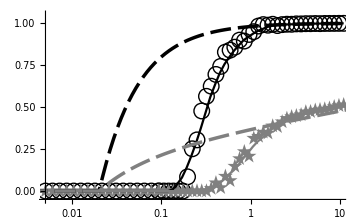

```mathematica
dat  = Import[localdir<>"task_1_Est_model_3_M_5_size_12_T_8000_ls_0.5_diff_a_1_muR_0.1_lambda_0.2_replicates_1_w_2.csv"][[;;-3]];
gd =Table[{π* dat[[i,2]]^2 * dat[[i,1]]*dat[[i,3]], dat[[i,4]]},{i , Length[dat]}];
sd =Table[{π*dat[[i,2]]^2 * dat[[i,1]] *dat[[i,3]], Mean[dat[[i,5;;8]]]},{i , Length[dat]}];

gd =FlattenAt[Prepend[gd, d0xy],1];
sd =FlattenAt[Prepend[sd, d0xy],1];

fig3a = ListLogLinearPlot[{gd,sd},ImageSize->Medium,Joined-> False, PlotMarkers->pm,PlotStyle->ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

gd1 = MovingAverage[gd,8] ;sd1 = MovingAverage[sd,8] ;

AppendTo[gd1, gd[[-1]]];
AppendTo[sd1, sd[[-1]]];

fig3aa =ListLogLinearPlot[{gd1,sd1},ImageSize->Medium,Joined-> True, PlotStyle->ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

fig3A =Show[fig3a,fig3aa,fig2d ]
```

```mathematica
Export[localdir<>"fig3a.jpg",fig3A,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure3\fig3a.jpg

### Figure 3b

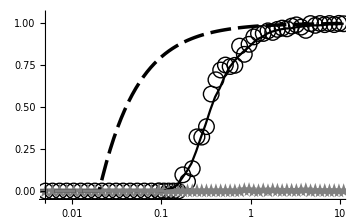

```mathematica
dat  = Import[localdir<>"task_1_Est_model_7_M_5_size_12_T_8000_ls_0.5_diff_a_1_muR_0.1_lambda_0.2_replicates_2_w_2.csv"][[;;-3]];
gd =Table[{π* dat[[i,2]]^2 * dat[[i,1]]*dat[[i,3]], dat[[i,4]]},{i , Length[dat]}];
sd =Table[{π*dat[[i,2]]^2 * dat[[i,1]] *dat[[i,3]], Mean[dat[[i,5;;8]]]},{i , Length[dat]}];

gd =FlattenAt[Prepend[gd, d0xy],1];
sd =FlattenAt[Prepend[sd, d0xy],1];

fig3b = ListLogLinearPlot[{gd,sd},ImageSize->Medium,Joined-> False, PlotMarkers->pm,PlotStyle-> ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

gd1 = MovingAverage[gd,8] ;sd1 = MovingAverage[sd,8] ;

AppendTo[gd1, gd[[-1]]];
AppendTo[sd1, sd[[-1]]];

fig3bb =ListLogLinearPlot[{gd1,sd1},ImageSize->Medium,Joined-> True, PlotStyle->ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

fig3B =Show[fig3b,fig3bb, fig2e]
```

```mathematica
Export[localdir<>"fig3b.jpg",fig3B,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure3\fig3b.jpg

### Figure 3c

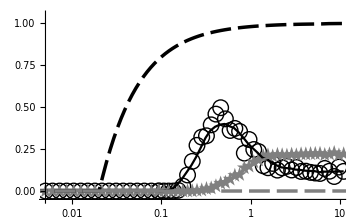

```mathematica
dat  = Import[localdir<>"task_1_Est_model_8_M_5_size_24_T_8000_ls_0.5_diff_a_1_muR_0.1_lambda_0.2_replicates_0_w_2.csv"][[;;-3]];
gd =Table[{π* dat[[i,2]]^2 * dat[[i,1]]*dat[[i,3]], dat[[i,4]]},{i , Length[dat]}];
sd =Table[{π*dat[[i,2]]^2 * dat[[i,1]] *dat[[i,3]], Mean[dat[[i,5;;8]]]},{i , Length[dat]}];

gd =FlattenAt[Prepend[gd, d0xy],1];
sd =FlattenAt[Prepend[sd, d0xy],1];

fig3c = ListLogLinearPlot[{gd,sd},ImageSize->Medium,Joined->False, PlotMarkers->pm,PlotStyle-> ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao];

gd1 = MovingAverage[gd,8] ;sd1 = MovingAverage[sd,8];
AppendTo[gd1, gd[[-1]]];
AppendTo[sd1, sd[[-1]]];

fig3cc =ListLogLinearPlot[{gd1,sd1},ImageSize->Medium,Joined-> True, PlotStyle->ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

fig3C =Show[fig3c,fig3cc,fig2e]
```

```mathematica
Export[localdir<>"fig3c.jpg",fig3C,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure3\fig3c.jpg

### Figure 3d

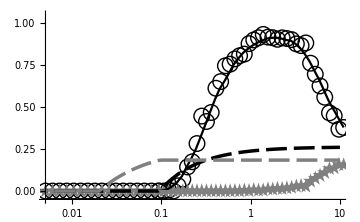

```mathematica
dat = Import[localdir<>"task_1_Est_model_7_M_5_size_24_T_8000_ls_0.5_diff_a_0.8_muR_0.1_lambda_0.2_replicates_0_w_2.csv"][[;;-3]];
gd =Table[{π* dat[[i,2]]^2 * dat[[i,1]]*dat[[i,3]], dat[[i,4]]},{i , Length[dat]}];
sd =Table[{π*dat[[i,2]]^2 * dat[[i,1]] *dat[[i,3]], Mean[dat[[i,5;;8]]]},{i , Length[dat]}];

gd =FlattenAt[Prepend[gd, d0xy],1];
sd =FlattenAt[Prepend[sd, d0xy],1];

fig3d = ListLogLinearPlot[{gd,sd},ImageSize->Medium,Joined-> False, PlotMarkers->pm,PlotStyle->ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

gd1 = MovingAverage[gd,8] ;sd1 = MovingAverage[sd,8] ;

AppendTo[gd1, gd[[-1]]];
AppendTo[sd1, sd[[-1]]];

fig3dd =ListLogLinearPlot[{gd1,sd1},ImageSize->Medium,Joined-> True, PlotStyle->ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

fig3D =Show[ fig3d,fig3dd,fig2f]
```

```mathematica
Export[localdir<>"fig3d.jpg",fig3D,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure3\fig3d.jpg